```mathematica
db=-(μ0/(4π))((J(a/2+b-y1))/((a/2+b-y1)^2+(z-z1)^2)^(3/2))
```

-(J (a/2+b-y1) μ0)/(4 π ((a/2+b-y1)^2+(z-z1)^2)^(3/2))

```mathematica
Integrate[db,{y1,-a/2,a/2}]
```

```mathematica
intz=Integrate[db,z1]
```

(J (z-z1) μ0)/(4 π (a/2+b-y1) √((a/2+b-y1)^2+(z-z1)^2))

```mathematica
∫dbⅆz1
```

(J (z-z1) μ0)/(4 π (a/2+b-y1) √((a/2+b-y1)^2+(z-z1)^2))

```mathematica
intz/.z1->∞
```

Infinity::indet: Indeterminate expression (0 J μ0 (-∞))/(π (a/2+b-y1)) encountered.

Indeterminate

```mathematica
ser=Normal@Series[Sin[x],{x,0,6}];
```

1-1/2 (-90 °+x)^2+1/24 (-90 °+x)^4

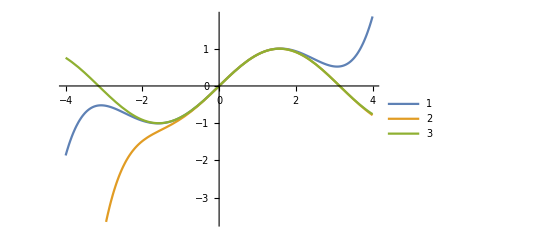

```mathematica
Plot[{ser,ser2,Sin[x]},{x,-4,4},PlotLegends->Automatic]
```